```mathematica
outDir=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"cpp/out"}];
SetDirectory[outDir]
```

/home/johansson/repo/polycubes/cpp/out

```mathematica
filter[list_,pattern_]:=Select[list,StringMatchQ[pattern]];
```

```mathematica
extractNMer[fileName_]:=Module[{r,c},{r,c}=StringCases[fileName,__~~"/out/"~~rule__~~"."~~color__~~"-mer"->{rule,color}]//First;
{r,Read[StringToStream[c],Number]}]
```

```mathematica
filter[{"aa","ab","ba"},".a"]
```

{}

```mathematica
all=FileNames["*", outDir];
all//Length
```

1050043

```mathematica
unbounded=filter[all,"*.oub*"];
unbounded//Length
```

958416

```mathematica
bounded=filter[all,"*-mer"];
bounded//Length
```

91627

```mathematica
filter[bounded,"*1-mer"]//Length
```

76124

```mathematica
filter[bounded,"*50-mer"]//Length
```

37

```mathematica
nMers=extractNMer /@ bounded;
```

```mathematica
Read[StringToStream[#],Number]&/@Take[Last/@nMers, 10]
```

{1,1,1,1,1,2,1,1,4,4}

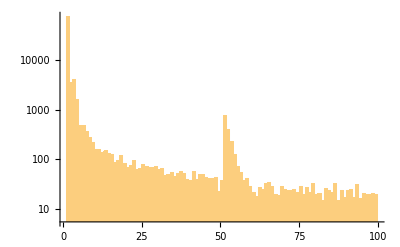

```mathematica
Histogram[Last/@nMers,ScalingFunctions->"Log",PlotRange->All]
```

```mathematica
Cases[nMers, {___,50}]
```

{{0006820006810e8481828680,50},{00800101090505098904068006068a030a8c,50},{0201060a05060f8e8f048105060b88890781,50},{02038a8f878e870b8a03860b87020b828e8b868188810880,50},{028802830a83830402898200040b010d8a0b07058b030501,50},{0507898e838801000f8900008f0e8e898302,50},{080387088e800d09070300818003838e0e09,50},{090903898e80040106880080,50},{090d01060580020607800f0a018e8c0c0401,50},{09850f86878b818289098383,50},{098e0006838d8a83088b8f06,50},{0a0f82048b078b830d0f000b,50},{0a8308068c8204028c018d84878c0b8c0500,50},{0a8e84088e86848803888f03,50},{0b860c838c018d830184830c,50},{0c0d8e018982888989818e89,50},{0d0f890f0e870c0406008284,50},{0f818f8e8683018a86010d02,50},{80820f080a8f03090c030c05838d828d07028001080a0d0d,50},{80858a8b058d878f8b8583808b0381868e8188058d848101,50},{808b0783840f0280850d0703,50},{820b0e0f098c028e01820408,50},{828584008b8b048201800781,50},{828b8c8f8380068c05838d87098c87830280,50},{830c8d0388000c008c828282,50},{838d8b840981838b88820303858e8f098a8f,50},{86818a0004028b008c878e8a89808d830487,50},{868a01880a848c098183028d,50},{878504028b0d038205020c0184830f8a8787,50},{88810e888303890c8001838f038f02898e0d,50},{8a8c8b83030502810d8b8702870003018b05,50},{8b8f8f008a888e898c85838e87858703080b,50},{8c06048d8b8f8303060881018b030b03048b090088838d8d,50},{8c08840b8d8a8e8e8b8701028d0501808e82,50},{8c810a0d090c0a8f08838708028c8e818200,50},{8d87890b8e0b8f09020903870286008a858d,50},{8d8b8009018d87828d830a09088c868881008000838d8f82,50}}

```mathematica
StringCases["/home/johansson/repo/polycubes/cpp/out/0000008e850b030707000306.4-mer",__~~"/out/"~~rule__~~"."~~type__~~"-mer"->{rule,type}]//First
```

{0000008e850b030707000306,4}

```mathematica
Partition[#,8]&/@Partition[IntegerDigits[FromDigits["0f018803038781850981080b",16],2],8*6]
```

{{{1,1,1,1,0,0,0,0},{0,0,0,1,1,0,0,0},{1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,0,1,1,1,0,0,0},{0,1,1,1,1,0,0,0}}}